# Script for SXS vs BoB comparison with Ωisco from FinalSpinMassQNM.nb and Ωi=Ωisco

## to accompany https://arxiv.org/abs/2205.14742

Author: Maria Babiuc-Hamilton and Dillon Buskirk

```mathematica
ClearAll["Global`*"];Off[General::spell];Remove["Global`*"]
SetOptions[Simplify,TimeConstraint->1000];
Unprotect[Sqrt]; Sqrt[x_^2]:=x; Protect[Sqrt];
$MinPrecision=$MachinePrecision;
```

Initial and final parameters

#Tune to SXS 0746

```mathematica
χ1=0.577899456899;
χ2=0.797826951453;
χfSXS=0.880726115;
MfSXS=0.918682416261;
```

From FinalSpinMassQNM.nb,  values for equal non-spinning binaries χf0Meq and Mfχ0Meq

```mathematica
χf =0.8805889975382539(*mean final spin for nonspinning individual BSs in the binary *)
Mf = 0.9223376556229705(*mean final mass for nonspinning individual BSs in the binary *)
```

0.880589

0.922338

We take the mean (Berti’s) value for frequency and Q from FinalSpinMassQNM.nb,  for l=2, m=2 mode:

```mathematica
MfωQNM = 0.6566451157454446(*0.6460523662254356*);
QQNM=5.003059966404495 (*4.796806396786768*);
MfωISCO=0.21233663555037466;
ωQNM=MfωQNM/Mf
τ = 2 QQNM/ωQNM
```

0.711936

14.0548

```mathematica
ωISCO=MfωISCO/Mf
```

0.230216

Freely chosen parameters

```mathematica
Ap=1;R=1;tp=0;
```

Starting BOB formulation

Quick check: Ωisco from FinalSpinMassQNM.nb, 1611.00332 eqs. (2)a,b,c and (3)a,b,c

```mathematica
Ωisco=(-0.091933*χf+0.097593)/(χf^2-2.4228*χf+1.4366) 
ωqnm=1.5251-1.1568*(1-χf)^0.1292
```

0.211823

0.646052

Clearly, the value of the ISCO frequency comes underestimated from the PN model, because we do not take into account the spin of the individual BH. While the resonance frequency might be overestimated by the analytic fit.

Now we can implement the BoB

Values taken directly from EccInsMerger_q1e0001. For this spin, rISCO=3.45425.

```mathematica
Ω3OrbPNISCO = 0.075297 ;
Ω3OrbPNISCOdot = 8.57723 10^-4 ;
```

```mathematica
Ωi = MfωISCO/2 (*Ω3OrbPNISCO*)
Ωidot = Ω3OrbPNISCOdot;
tp =0;
ΩQNM = ωQNM/2
```

0.106168

0.355968

```mathematica
ti=tp-τ/2 Log[(ΩQNM^4-Ωi^4)/(2*τ*Ωi^3 Ωidot)-1]
```

-44.3562

```mathematica
(*Ap=1.068*(1-Mf)^0.8918*)
```

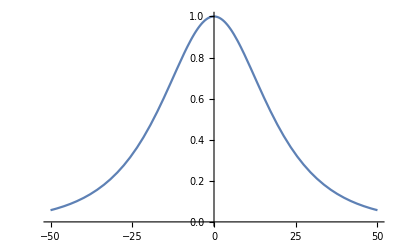

```mathematica
ψ4[t_]:=Ap*Sech[(t-tp)/τ];
Plot[ψ4[t],{t,-50,50}]
```

```mathematica
kB=((ΩQNM^4-Ωi^4)/(1-Tanh[(ti-tp)/τ]))
```

0.00797903

```mathematica
ΩB[t_]:=(Ωi^4+kB(Tanh[(t-tp)/τ]-Tanh[(ti-tp)/τ]))^(1/4)
```

```mathematica
ωBoB[t_]:=2*ΩB[t];
```

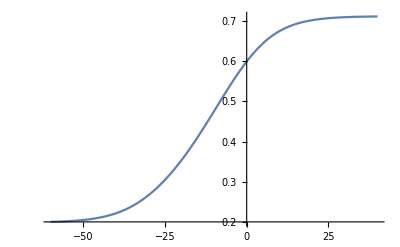

```mathematica
Plot[ωBoB[t],{t,-60,40}]
```

```mathematica
Kappap=(Ωi^4+kB(1-Tanh[(ti-tp)/τ]))^(1/4)
```

0.355968

```mathematica
Kappam=(Ωi^4-kB(1+Tanh[(ti-tp)/τ]))^(1/4)
```

0.0995333

```mathematica
arctanp[t_]:=Kappap*τ*(ArcTan[(ΩB[t]/Kappap)]-ArcTan[Ωi/Kappap])
arctanm[t_]:=Kappam*τ*(ArcTan[ΩB[t]/Kappam]-ArcTan[Ωi/Kappam])
arctanhp[t_]:=Kappap*τ*(ArcTanh[ΩB[t]/Kappap]-ArcTanh[Ωi/Kappap])
arctanhm[t_]:=Kappam*τ*(ArcTanh[ΩB[t]/Kappam]-ArcTanh[Ωi/Kappam])
```

```mathematica
PhaseB[t_]:=arctanp[t]+arctanhp[t]-arctanm[t]-arctanhm[t]
```

```mathematica
ϕBoB[t_]:=2*PhaseB[t]
```

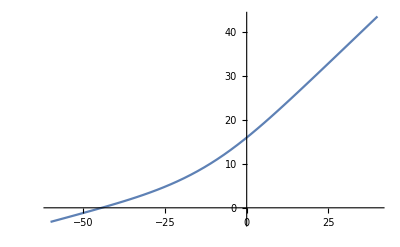

```mathematica
Plot[ϕBoB[t],{t,-60,40}]
```

```mathematica
AmpBoB[t_]:=Abs[ψ4[t]]/ωBoB[t]^2
```

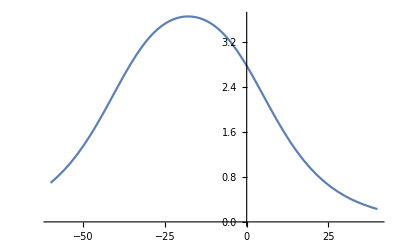

```mathematica
Plot[AmpBoB[t],{t,-60,40}]
```

```mathematica
MaxAmpBoB=FindMaxValue[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

3.65979

```mathematica
tpBoB = First@FindArgMax[{AmpBoB[t],-40<=t<=0},{t,-20}]
```

-17.9107

```mathematica
hBoB[t_]:=-AmpBoB[t]*Exp[-ⅈ* ϕBoB[t]]
```

Note that the maximum in amplitude and maximum in the rate of variation of the frequency is not the same!

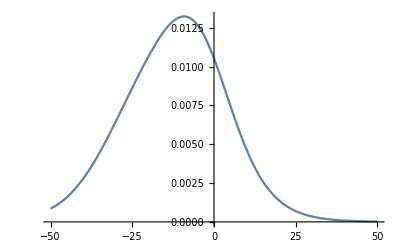

```mathematica
Plot[ωBoB'[t],{t,-50,50}]
```

```mathematica
tfBoB=t/.FindRoot[ωBoB''[t]==0,{t,-20,10}]
```

-9.17457

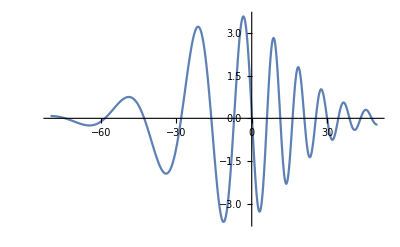

```mathematica
Plot[Re[hBoB[t+tfBoB]],{t,-80,50}]
```

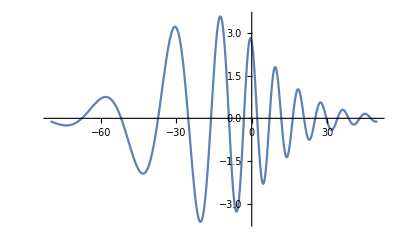

```mathematica
Plot[Re[hBoB[t]],{t,-80,50}]
```

```mathematica
MaxRehBoB = FindMaxValue[{Re[hBoB[t]],-20<=t<=0},{t,-10}]
```

3.58454

```mathematica
thBoB = First@FindArgMax[{Re[hBoB[t]],-40<=t<=0},{t,-10}]
```

-12.4865

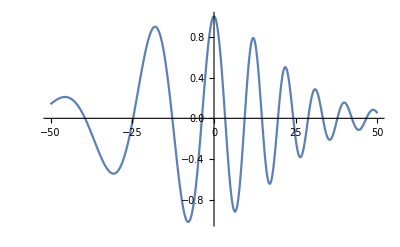

```mathematica
Plot[Re[hBoB[t+thBoB ]]/MaxRehBoB,{t,-50,50}]
```

```mathematica
Δtf = tfBoB-tpBoB
```

8.73614

```mathematica
Δtp = thBoB-tpBoB
```

5.4242

```mathematica
SXS0746Data=Import["/Users/babiuc/BBH0746_22.dat","Table"]
```

{{-107.805,-0.000106162,-0.00278313},{-106.865,-0.000102975,-0.0027943},16653,{5234.,-0.0000204591,4.94743×10^-6},{5234.1,-0.0000185512,5.81771×10^-6}}
 |  |  |  |

```mathematica
(*SXS0746Data=Import["/Users/babiuc/Dropbox/StudentResearch/Dillon/GradWork/Code/Data/SXS_BBH_0746_N4_Y_l2_m2.txt","Table","FieldSeparators"->","]*)
```

```mathematica
SXS0746DataTime=SXS0746Data[[All,1]];
```

```mathematica
ReSXS0746DataStrain=SXS0746Data[[All,2]];
```

```mathematica
MaxReSXS0746DataStrain=Max[ReSXS0746DataStrain]
```

0.386693

```mathematica
MinReSXS0746DataStrain=Min[ReSXS0746DataStrain]
```

-0.37401

```mathematica
ImSXS0746DataStrain=SXS0746Data[[All,3]];
```

```mathematica
MaxImSXS0746DataStrain=Max[ImSXS0746DataStrain]
```

0.383055

```mathematica
MinImSXS0746DataStrain=Min[ImSXS0746DataStrain]
```

-0.382347

```mathematica
AmpSXS0746DataStrain = Sqrt[ReSXS0746DataStrain^2+ImSXS0746DataStrain^2];
```

```mathematica
MaxAmpSXS0746DataStrain=Max[Abs[AmpSXS0746DataStrain]]
```

0.386724

```mathematica
Position[ReSXS0746DataStrain ,_?(#>0.999999*MaxReSXS0746DataStrain&)]
```

{{15238}}

```mathematica
Position[AmpSXS0746DataStrain ,_?(#>0.999999*MaxAmpSXS0746DataStrain&)]
```

{{15238}}

```mathematica
SXS0746DataTimeShift=SXS0746DataTime-SXS0746DataTime[[15238]];
```

```mathematica
AmpSXS0746DataStrainNorm = AmpSXS0746DataStrain/MaxAmpSXS0746DataStrain;
```

```mathematica
AmpSXS0746DataShift=Transpose[{SXS0746DataTimeShift,AmpSXS0746DataStrainNorm }];
```

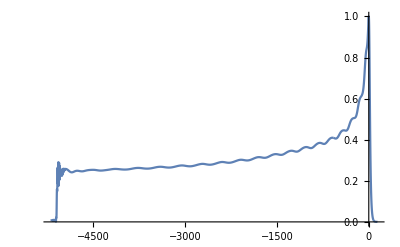

```mathematica
ListPlot[AmpSXS0746DataShift[[All,1;;2]],Joined->True]
```

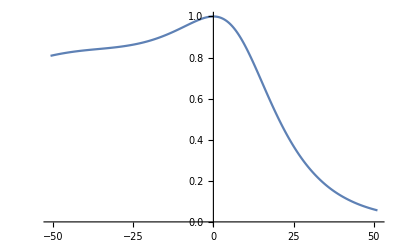

```mathematica
ListLinePlot[AmpSXS0746DataShift[[14730;;15750]]]
```

```mathematica
ReSXS0746DataStrainNorm = ReSXS0746DataStrain/MaxReSXS0746DataStrain;
ImSXS0746DataStrainNorm = ImSXS0746DataStrain/MaxImSXS0746DataStrain;
```

```mathematica
pReSXS0746DataShift=Transpose[{SXS0746DataTimeShift,+ReSXS0746DataStrainNorm}];
```

```mathematica
mReSXS0746DataShift=Transpose[{SXS0746DataTimeShift,-ReSXS0746DataStrainNorm }];
```

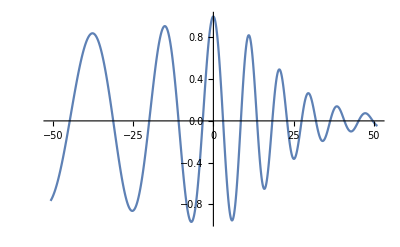

```mathematica
ListPlot[pReSXS0746DataShift[[14730;;15750]],Joined->True]
```

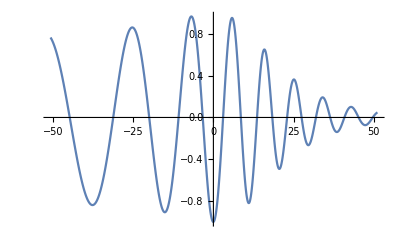

```mathematica
ListPlot[mReSXS0746DataShift[[14730;;15750]],Joined->True]
```

tfBoB, tpBoB, thBoB

```mathematica
tfBoB
 tpBoB
 thBoB
```

-9.17457

-17.9107

-12.4865

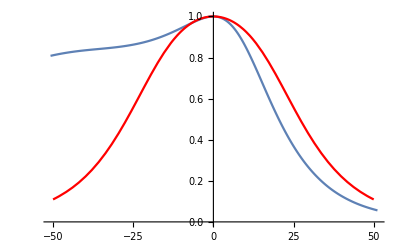

```mathematica
Show[ListPlot[AmpSXS0746DataShift[[14730;;15750]],Joined->True],Plot[AmpBoB[t+tpBoB]/MaxAmpBoB,{t,-50,50},PlotStyle->Red]]
```

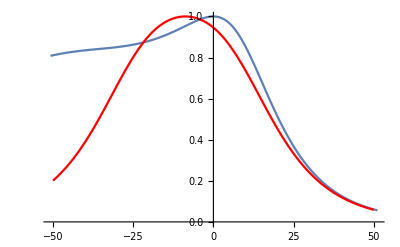

```mathematica
Show[ListPlot[AmpSXS0746DataShift[[14730;;15750]],Joined->True],Plot[AmpBoB[t+tfBoB]/MaxAmpBoB,{t,-50,50},PlotStyle->Red]]
```

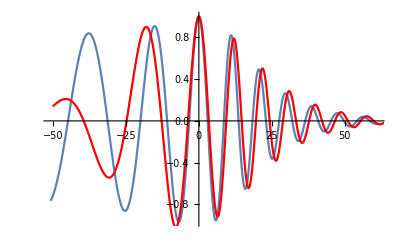

```mathematica
Show[ListPlot[pReSXS0746DataShift[[14730;;15850]],Joined->True],
Plot[Re[hBoB[t+thBoB]]/MaxRehBoB,{t,-50,70},PlotStyle->Red]]
```

```mathematica
ArgSXS= Flatten[ArcTan[ImSXS0746DataStrainNorm/ReSXS0746DataStrainNorm]];
```

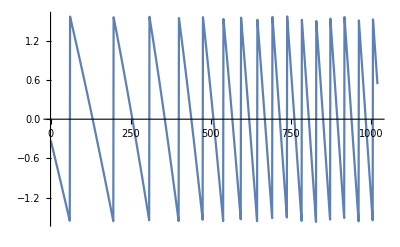

```mathematica
ListPlot[ArgSXS[[14730;;15750]],Joined->True]
```

Function taken from https://community.wolfram.com/groups/-/m/t/1340126

```mathematica
Unwrap[lst_List]:=Unwrap[lst,2Pi] (*phase jumps of 2Pi is the default because of trigonometric funtions*)
Unwrap[lst_List,Δ_]:=Unwrap[lst,Δ,Scaled[0.5]] (*default tolerance is half the phase jump Δ*)
Unwrap[lst_List,Δ_,tolerance_]:=Module[{tol,jumps},tol=If[Head[tolerance]===Scaled,Δ tolerance[[1]],tolerance];
jumps=Differences[lst];
jumps=-Sign[jumps]Unitize[Chop[Abs[jumps],tol]];
jumps=Δ Prepend[Accumulate[jumps],0];
jumps+lst]
```

```mathematica
unwrapArgSXS=Unwrap[ArgSXS,3];
```

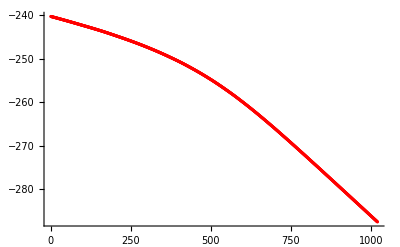

```mathematica
unwrapArgSXSFiltered=MeanFilter[unwrapArgSXS,100];
ListPlot[unwrapArgSXSFiltered[[14730;;15750]],PlotStyle->Red]
```

```mathematica
ϕSXS=Transpose[{SXS0746DataTimeShift,Flatten[-unwrapArgSXS]}];
ϕSXSfiltered=Transpose[{SXS0746DataTimeShift,Flatten[-unwrapArgSXSFiltered]}];
```

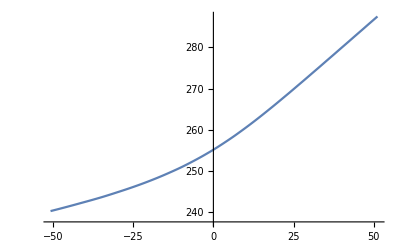

```mathematica
ListLinePlot[ϕSXSfiltered[[14730;;15750]]]
```

```mathematica
interpϕSXS=Interpolation[ϕSXS[[14730;;15750]],InterpolationOrder->4]
interpϕSXSfiltered=Interpolation[ϕSXSfiltered[[14700;;15800]],InterpolationOrder->4]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

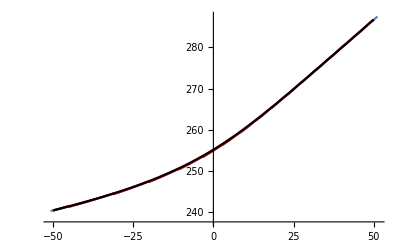

```mathematica
Show[ListPlot[ϕSXS[[14730;;15750]],Joined->True],Plot[interpϕSXS[t],{t,-50,50},PlotStyle->Red], Plot[interpϕSXSfiltered[t],{t,-50,50},PlotStyle->Black]]
```

```mathematica
ΔϕSXSBoB =interpϕSXSfiltered[0]-Re[ϕBoB[tfBoB]]
```

244.254

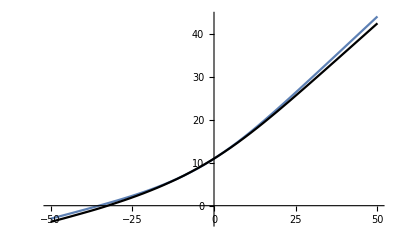

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

https://mathematica.stackexchange.com/questions/126302/how-to-get-a-smooth-derivative-graphic

```mathematica
dϕSXS=Differences[Last/@ϕSXSfiltered]
```

{0.0116856,0.0119525,0.0131447,0.0144768,0.0151795,0.0153317,0.0151634,16642,0.035514,0.0356431,0.0357708,0.0358962,0.0360181,0.0361361,0.0362491}
 |  |  |  |

```mathematica
dϕSXS=dϕSXS/Differences[First/@ϕSXSfiltered]
```

{0.0124237,0.0127075,0.013975,0.0153912,0.0161383,0.0163357,0.0161212,16642,0.355198,0.356489,0.357766,0.35902,0.36024,0.36142,0.36255}
 |  |  |  |

```mathematica
dϕSXSfiltered=MeanFilter[dϕSXS,100]
```

{0.0136955,0.0137791,0.0138635,0.0139456,0.0140325,0.0141175,0.0142032,16642,0.356843,0.354078,0.351265,0.348401,0.345483,0.342509,0.339475}
 |  |  |  |

```mathematica
{dϕSXS,dϕSXSfiltered}=Transpose[{Most[First/@ϕSXSfiltered],#}]&/@{dϕSXS,dϕSXSfiltered}
```

{{{-5200.06,0.0124237},{-5199.12,0.0127075},{-5198.18,0.013975},16650,{141.545,0.36024},{141.645,0.36142},{141.745,0.36255}},{1}}
 |  |  |  |

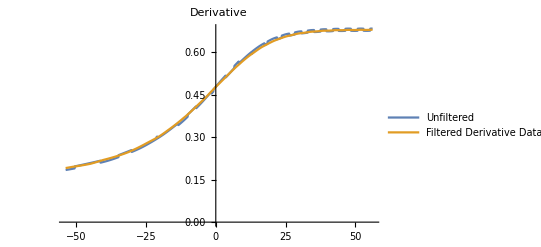

```mathematica
ListLinePlot[{dϕSXS[[14700;;15800]],dϕSXSfiltered[[14700;;15800]]},PlotStyle->{Thin,Thick},PlotLegends->{"Unfiltered","Filtered Derivative Data"},PlotLabel->"Derivative"]
```

```mathematica
interpωSXSfiltered=Interpolation[dϕSXSfiltered[[14700;;15800]],InterpolationOrder->4]
```

InterpolatingFunction[…]

```mathematica
interpωSXSfiltered[0]
```

0.476934

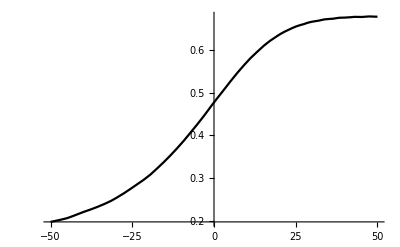

```mathematica
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->Black]
```

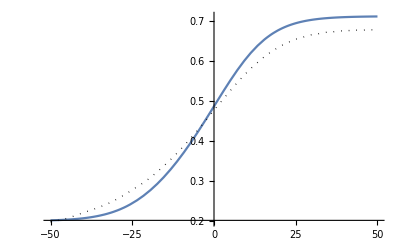

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->{Black,Dotted, Thick}],
PlotRange->All]
```

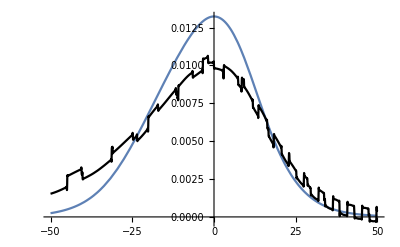

```mathematica
Show[Plot[ωBoB'[t+tfBoB],{t,-50,50}],
Plot[interpωSXSfiltered'[t],{t,-50,50},PlotStyle->{Black}],
PlotRange->All]
```

Plots for paper: SXS-BoB comparison

```mathematica
Show[ListPlot[AmpSXS0746DataShift[[14730;;15750]],Joined->True],Plot[AmpBoB[t+tpBoB]/MaxAmpBoB,{t,-50,50},PlotStyle->Red]]
```

-Graphics-

```mathematica
Show[Plot[ϕBoB[t+tfBoB],{t,-50,50}],
Plot[interpϕSXSfiltered[t]-ΔϕSXSBoB,{t,-50,50},PlotStyle->Black],
PlotRange->All]
```

-Graphics-

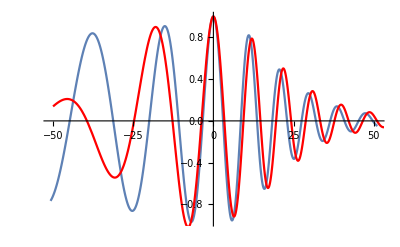

```mathematica
Show[ListPlot[pReSXS0746DataShift[[14730;;15750]],Joined->True],
Plot[Re[hBoB[t+thBoB]]/MaxRehBoB,{t,-50,70},PlotStyle->Red]]
```

```mathematica
Show[Plot[ωBoB[t+tfBoB],{t,-50,50}],
Plot[interpωSXSfiltered[t],{t,-50,50},PlotStyle->{Black,Dotted, Thick}],
PlotRange->All]
```

-Graphics-

## Plotting Work

```mathematica
dt=0.01;
```

```mathematica
tArray=Table[t,{t,-50,50,dt}];
```

```mathematica
tArray1=Table[t,{t,-50,70,dt}];
```

```mathematica
AmpBoBTab=Table[AmpBoB[t+tpBoB]/AmpBoBMax,{t,-50,50,dt}];
```

```mathematica
AmpBoBvsTimeTab=Partition[Riffle[tArray,AmpBoBTab],2];
```

```mathematica
PrependTo[AmpBoBvsTimeTab, {"t(M)", "hAmp(t)"}];
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/AmpBoBforSXScomp.txt",AmpBoBvsTimeTab]*)
```

```mathematica
SXSAmpData=AmpSXS0746DataShift[[14750;;15750]];
```

```mathematica
PrependTo[SXSAmpData, {"t(M)", "hAmp(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/AmpSXSforSXScomp.txt",SXSAmpData]
```

dropbox/dillon/paperplottingwork/AmpSXSforSXScomp.txt

```mathematica
hBoBTab=Table[Re[hBoB[t+thBoB]]/AmpBoBMax,{t,-50,70,dt}];
```

```mathematica
hBoBvsTimeTab=Partition[Riffle[tArray1,hBoBTab],2];
```

```mathematica
PrependTo[hBoBvsTimeTab, {"t(M)", "h(t)"}];
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/hBoBforSXScomp.txt",hBoBvsTimeTab]*)
```

```mathematica
SXShData=mReSXS0746DataShift[[14750;;15850]];
```

```mathematica
PrependTo[SXShData, {"t(M)", "h(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/hSXSforSXScomp.txt",SXShData]
```

dropbox/dillon/paperplottingwork/hSXSforSXScomp.txt

```mathematica
BoBphasetab=Table[ϕBoB[t+tfBoB],{t,-50,50,dt}];
```

```mathematica
BoBphasevstimetab=Partition[Riffle[tArray,BoBphasetab],2];
```

```mathematica
PrependTo[BoBphasevstimetab, {"t(M)", "ϕ(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiBoBforSXScomp.txt",BoBphasevstimetab]
```

dropbox/dillon/paperplottingwork/phiBoBforSXScomp.txt

```mathematica
SXSphasetab=Table[interpϕSXSfiltered[t]-ΔϕSXSBoBfiltered,{t,-50,50,dt}];
```

```mathematica
SXSphasevstimetab=Partition[Riffle[tArray,SXSphasetab],2];
```

```mathematica
PrependTo[SXSphasevstimetab, {"t(M)", "ϕ(t)"}];
```

```mathematica
Export["dropbox/dillon/paperplottingwork/phiSXSforSXScomp.txt",SXSphasevstimetab]
```

dropbox/dillon/paperplottingwork/phiSXSforSXScomp.txt